## Graphing the Effective Potential for Light

We derived

1/b^(*2)=1/b^(*2)((d r_shell)/(d t_shell))^2+v_(effective,light)^(*2)(r^*)

Where

v_(effective,light)^(*2)(r^*)≡(1-2/r^*)/r^(*2)

Let’s graph this thing

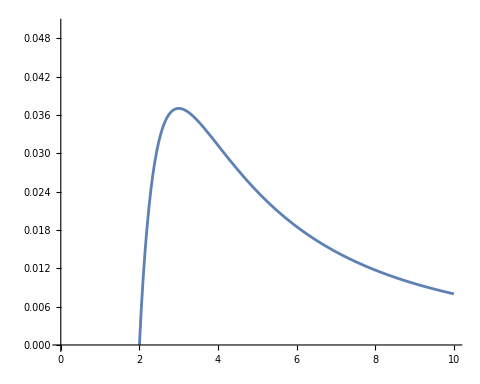

```mathematica
vEffectiveLight[r_]:=(1-2/r)/r^2

Plot[vEffectiveLight[r],{r,0,10}, PlotRange->{{0,10},{0,0.05}},AspectRatio->0.8,GridLines->{Range[0,10,1],Range[1/3,4/3,1/3]/27}]
```